```mathematica
(*generation of the phase distribution to be used in the calculation of the field components*)
ArcTan[0,0]:=0;
n=10;
m=10;
For[i=1;t=x,i^1<n-1,i++,t=i^1+0;
For[j=1;tt=y,j^1<m-1,j++,tt=j+0;{ss=Table[Sqrt[i^2+j^2],{i,Range[-5,5,0.1]},{j,Range[-5,5,0.1]}],at=Table[Arg[Complex[i,j]],{i,Range[-5,5,0.1]},{j,Range[-5,5,0.1]}],ttt=Sin[2*at]}]];
```

SetDelayed::write: Tag ArcTan in ArcTan[0, 0] is Protected.

```mathematica
(*Trapezoid Rule*)
n=10;S0=0;u=2;alpha=0.7;S1=0;S2=0;
x=ss;
For[i=1;p=x,i^1<n,i++,p=x^1;{aa=Table[S0=S0+(Cos[i/n])^(1/2) Sin[i/n] (1+Cos[i/n]) BesselJ[0,(p*Sin[i/n]/Sin[1.3])] Exp[(Cos[i/n])*(I+u)/(Sin[alpha])^2],{i,n}],bb=Table[S1=S1+(Cos[i/n])^(1/2) (Sin[i/n])^2 BesselJ[1,(p*Sin[i/n]/Sin[1.3])] Exp[(Cos[i/n])*(I+u)/(Sin[alpha])^2],{i,n}],cc=Table[S2=S2+(Cos[i/n])^(1/2) Sin[i/n] (1-Cos[i/n]) BesselJ[2,(p*Sin[i/n]/Sin[1.3])] Exp[(Cos[i/n])*(I+u)/(Sin[alpha])^2],{i,n}]}]
```

```mathematica
I0=(alpha/n)*(S0+0.5*(Cos[alpha]^0.5)*Sin[alpha]*(1+Cos[alpha])*BesselJ[0,ss]*Exp[Cos[alpha]*(I+u)/(Sin[alpha])^2]);
I1=(alpha/n)*(S1+0.5*(Cos[alpha]^0.5)*(Sin[alpha]^2)*BesselJ[1,ss]*Exp[Cos[alpha]*(I+u)/(Sin[alpha])^2]);
I2=(alpha/n)*(S2+0.5*(Cos[alpha]^0.5)*Sin[alpha]*(1-Cos[alpha])*BesselJ[2,ss]*Exp[Cos[alpha]*(I+u)/(Sin[alpha])^2]);

Ex=I0+I2*Cos[2*at];
Ey=I2*Sin[2*at];
Ez=-2 I1*Cos[at];
E=Abs[Ex]^2+Abs[Ey]^2+Abs[Ez]^2
```

Set::wrsym: Symbol ⅇ is Protected.

{{213.428,225.734,238.698,252.454,267.157,282.987,300.144,318.849,339.339,361.87,386.706,414.12,444.387,«76»,414.12,386.706,361.87,339.339,318.849,300.144,282.987,267.157,252.454,238.698,225.734,213.428},«99»,{«18»,«99»,«18»}}

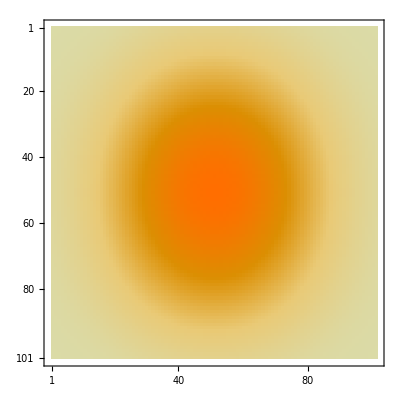

```mathematica
MatrixPlot[%29]
```